### Resonance Plot

```mathematica
ResPlotColours={
{ColorData["Legacy","Black"],AbsoluteThickness[3]},
{ColorData["Legacy","Red"],AbsoluteThickness[2.75]},
{ColorData["Legacy","Blue"],AbsoluteThickness[2.5]},
{ColorData["Legacy","Green"],AbsoluteThickness[2.25]},
{ColorData["Legacy","Orange"],AbsoluteThickness[2]},
{ColorData["Legacy","Red"],AbsoluteThickness[1]},
{ColorData["Legacy","Blue"],AbsoluteThickness[0.9]},
{ColorData["Legacy","Green"],AbsoluteThickness[0.8]},
{ColorData["Legacy","Orange"],AbsoluteThickness[0.7]},
{ColorData["Legacy","YellowGreen"],AbsoluteThickness[0.6]},
{RGBColor[.6,1,0],AbsoluteThickness[.2]},
{RGBColor[.8,1,0],AbsoluteThickness[.2]},
{RGBColor[1,1,0],AbsoluteThickness[.2]},
{RGBColor[1,1,.2],AbsoluteThickness[.2]},
{RGBColor[1,1,.4],AbsoluteThickness[.2]},
{RGBColor[1,1,.6],AbsoluteThickness[.2]},
{RGBColor[1,1,.8],AbsoluteThickness[.2]},
{RGBColor[1,1,1],AbsoluteThickness[.2]}};
```

```mathematica
LegendData:=MapIndexed[{Directive[#],ToString[#2[[1]]]}&,ResPlotColours];
```

```mathematica
ResonanceEquationsAtOrder[range_,resorder_,periodicity_]:=Union[Flatten[Table[ResEqn@@@ResNumAtOrder[resorder]/.l->periodicity ,{pvalue,First[PValues[ResNumAtOrder[resorder],range,periodicity]],Last[PValues[ResNumAtOrder[resorder],range,periodicity]]}]]]
```

```mathematica
ResonanceEquations[range_,orderstart_,orderend_,periodicity_]:=Union[Flatten[Table[ResonanceEquationsAtOrder[range,n,periodicity],{n,orderstart,orderend}]]]
```

```mathematica
ResonancePlot[range_,orderstart_,orderend_,periodicity_,opts___]:=Block[{optPlot,optShow,legend,RangePoints,l,pvalue,x,y,m,n},
legend=ResonanceLegend/.{opts}/.{ResonanceLegend->False};
optShow=Sequence@@FilterRules[Flatten[{opts}],Options[Show]];
optPlot=Sequence@@FilterRules[Flatten[{opts}],Options[ContourPlot]];

ResEqn[m_,n_]:=(m x+n y==l pvalue);
ResNumAtOrder[r_]:=Flatten[Table[{{x,r-x},{x,x-r}},{x,0,r}],1];RangePoints:={{range[[1,1]]-10^-6,range[[2,1]]+10^-6},{range[[1,1]]-10^-6,range[[2,2]]+10^-6},{range[[1,2]]-10^-6,range[[2,1]]+10^-6},{range[[1,2]]-10^-6,range[[2,2]]+10^-6}};
PValues[resnums_,r_,p_]:=Block[{equations={(m x+n y)/l}},
Flatten[{Floor[Min[#]],Ceiling[Max[#]]}&/@{Flatten[equations/.l->p/.{m->#[[1]],n->#[[2]]}&/@resnums/.{x->#[[1]],y->#[[2]]}&/@RangePoints]}]];
Show[Reverse[Table[ContourPlot[Evaluate[ResonanceEquationsAtOrder[range,n,periodicity]],{x,range⟦1,1⟧-10^-6,range⟦1,2⟧+10^-6},{y,range⟦2,1⟧-10^-6,range⟦2,2⟧+10^-6},ContourStyle->{ResPlotColours⟦n⟧},Evaluate[optPlot],PlotLegends->If[n==1&&legend==True,ResonanceLegend[orderstart,orderend],None]],{n,orderstart,orderend,1}]],optShow]]
```

```mathematica
ResonanceLegend[min_,max_]:=LineLegend[LegendData[[min;;max,1]],LegendData[[min;;max,2]],LegendLabel->"Resonance Order"]
```

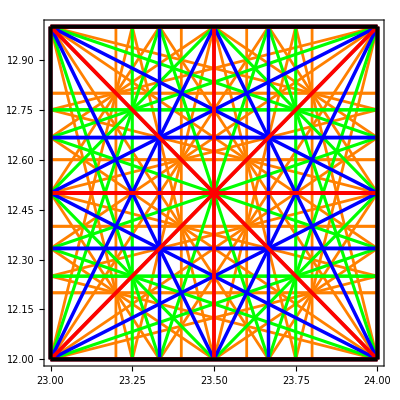

```mathematica
ResonancePlot[{{23,24},{12,13}},1,5,1,ResonanceLegend->False]
```